```mathematica
k4rob =Select[ , Last[#]>100&];
```

```mathematica
k4reg= Select[,Last[#]>100&];
```

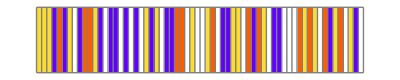
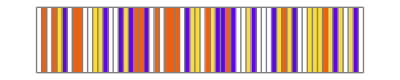
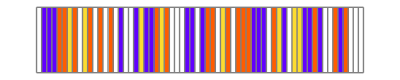
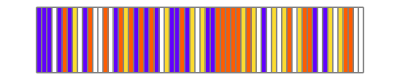
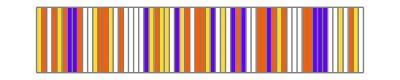
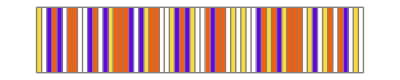
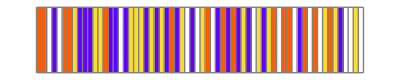
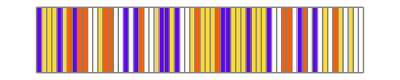

```mathematica
plotrule/@ k4reg[[All,1]]
```

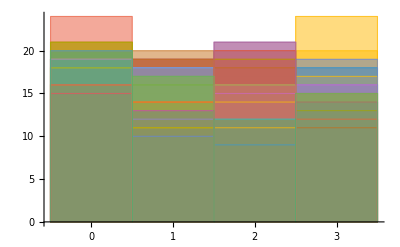

```mathematica
Histogram[Module[{digits, n, k, r},
{n, k, r} =interpretrule[#];
digits = IntegerDigits[n, k, k^(2r+1)]]&/@ k4reg[[All, 1]]]
```

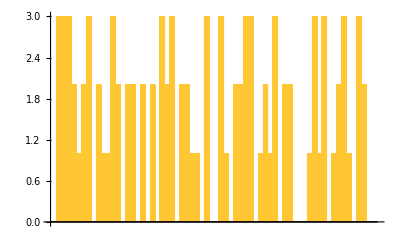
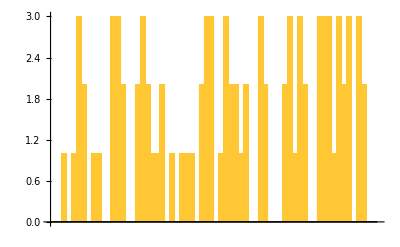
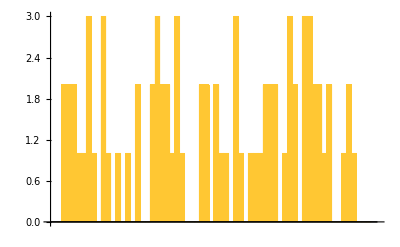
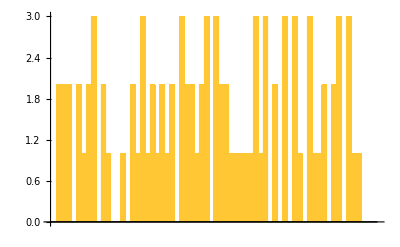
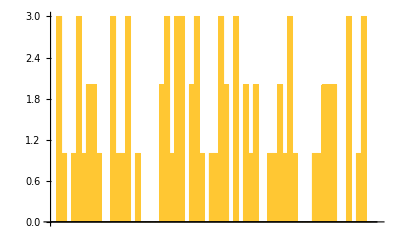
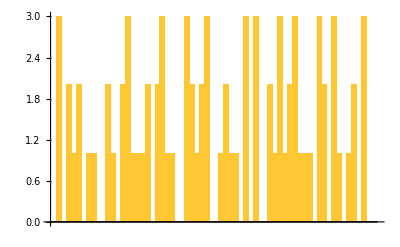
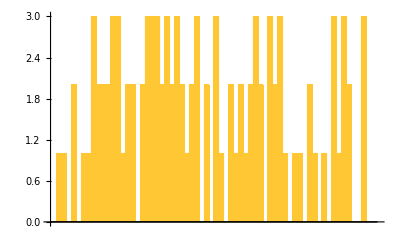
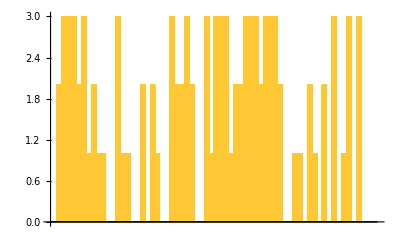

```mathematica
Map[BarChart, Module[{digits, n, k, r},
{n, k, r} =interpretrule[#];
digits = IntegerDigits[n, k, k^(2r+1)]]&/@ k4reg[[All, 1]]]
```

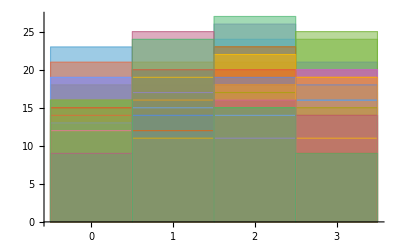

```mathematica
Histogram[RandomChoice[{0, 1, 2, 3}, {Length[k4reg], 4^(2*1+1)}]]
```

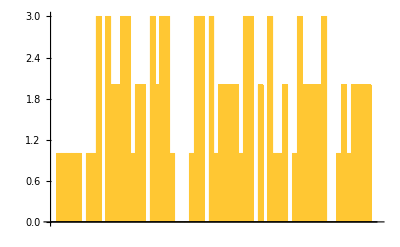
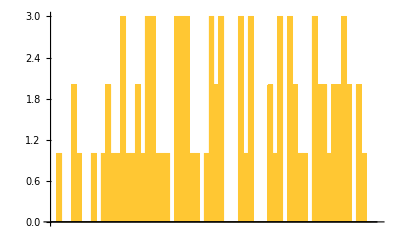
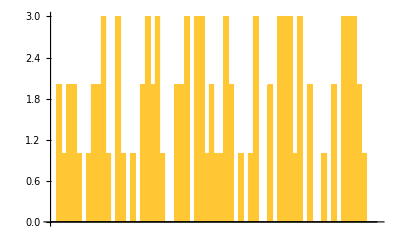
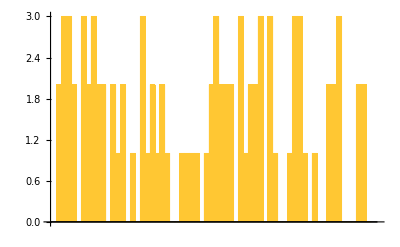
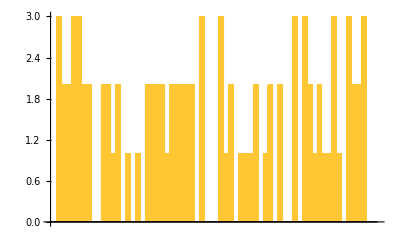
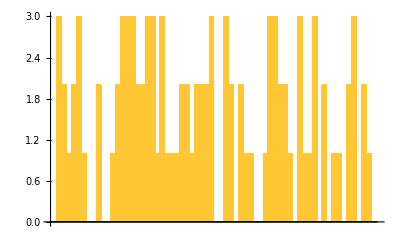
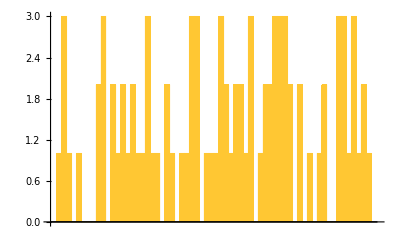
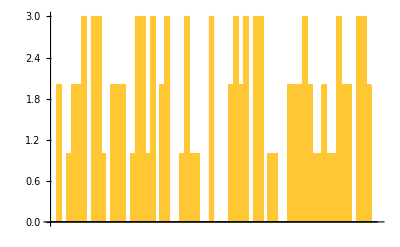

```mathematica
BarChart/@(RandomChoice[{0, 1, 2, 3}, {Length[k4reg], 4^(2*1+1)}])
```

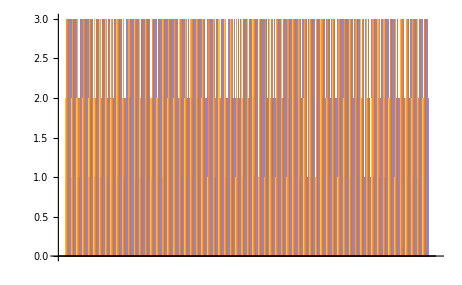

```mathematica
BarChart[Transpose[(RandomChoice[{0, 1, 2, 3}, {Length[k4reg], 4^(2*1+1)}])]]
```

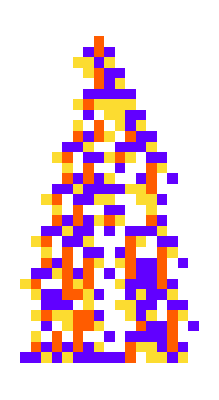
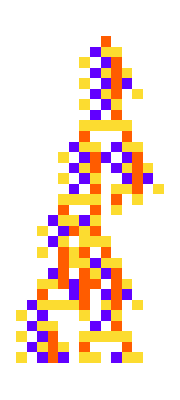
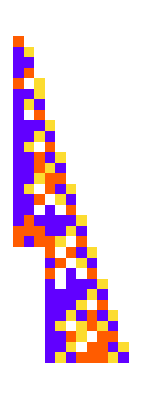
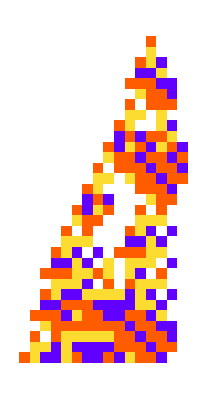
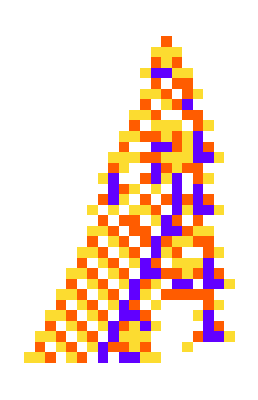
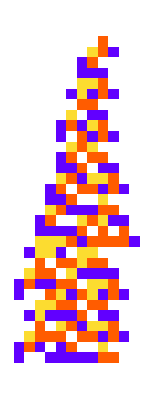
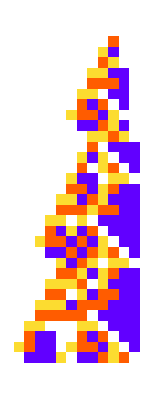
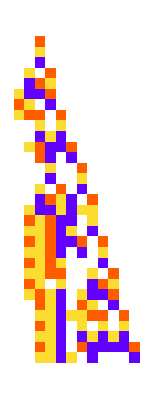

```mathematica
ArrayPlot[CellularAutomaton[#, {{1}, 0}, 30], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@k4reg[[All, 1]]
```

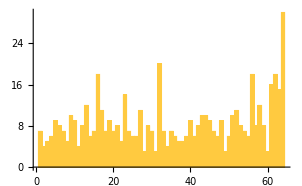

```mathematica
Histogram[Catenate[Module[{digits, n, k, r},
{n, k, r} =interpretrule[#];
digits = IntegerDigits[n, k, k^(2r+1)];
Flatten[Position[digits, 0]]]&/@ k4reg[[All, 1]]], {1}]
```

```mathematica
RulePlot[]
```

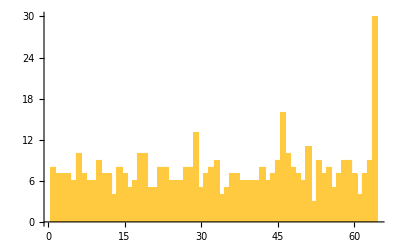

```mathematica
Histogram[Catenate[Flatten[Position[#, 0]]&/@(Append[#, 0]&/@RandomChoice[{0, 1, 2, 3}, {Length[k4reg] , 4^(2*1+1) - 1}])], {1}]
```

```mathematica
plotrule/@k4reg[[All, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
RulePlot[CellularAutomaton[#],ColorRules-> {{"[◼]", "CustomStyleData"}}["Colors"]]&/@ k4reg[[All, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Comparisons

#### Plots

```mathematica
ArrayPlot[CellularAutomaton[#,{{1}, 0}, 200], ColorRules-> {{"[◼]", "CustomStyleData"}}["Colors"]]& /@k4reg[[All, 1]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ArrayPlot[CellularAutomaton[{FromDigits[#, 4], 4, 1}, {{1}, 0}, 200], ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]]&/@(Append[#, 0]&/@RandomChoice[{0, 1, 2, 3}, {Length[k4reg] , 4^(2*1+1) - 1}])
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Comparing those found by search to those found by adaptation